# Force-free Current Sheet

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};

saveP[name_,p_,fmt_:".svg"]:=Export["../figures/"<>name<>fmt,p];

SaveP[suffix_:""]:=Module[{},
ExportP["profiles"<>suffix,p1];
ExportP["J_profiles"<>suffix,p2];
ExportP["s1_profiles"<>suffix,pn1];
]

saveName[c_]:=StringReplace[
StringRiffle[ToString/@c,"_"]," -> "->"="
]
```

## MHD

```mathematica
Vx[z_]:=V0 Cos[φ[z]]
Vy[z_]:=V0 Sin[φ[z]]
Bx[z]:=B0 Cos[φ[z]]
By[z]:=B0 Sin[φ[z]]

V:={Vx[z],Vy[z],Vz[z]};
B:={Bx[z],By[z],Bz};
r={x,y,z};
J:=Curl[B,r]
(*J:={Jx,Jy,Jz}*)
eqM:=Γ  D[V,z]+Grad[p[z],r]==J×B
eqM
```

{-V0 Γ Sin[φ[z]] φ'[z],V0 Γ Cos[φ[z]] φ'[z],p'[z]+Γ Vz'[z]}=={-B0 Bz Sin[φ[z]] φ'[z],B0 Bz Cos[φ[z]] φ'[z],0}

```mathematica
eqM1:=-V0 Γ Sin[φ[z]] φ'[z]==-B0 Bz Sin[φ[z]] φ'[z]//Simplify
eqM2:=V0 Γ Cos[φ[z]] φ'[z]==B0 Bz Cos[φ[z]] φ'[z]//Simplify
{eqM1,eqM2}
```

{(B0 Bz-V0 Γ) Sin[φ[z]] φ'[z]==0,(B0 Bz-V0 Γ) Cos[φ[z]] φ'[z]==0}

## Multiple - Fluid

```mathematica
(* Change the directory to the current file location *)
SetDirectory@NotebookDirectory[];
```

```mathematica
Bx:=B0 Cos[φ[z]];
By:=B0 Sin [φ[z]]
u1x:=u1 Cos [φ[z]];
u1y:=u1 Sin[φ[z]];

assums={B0≠0};
notationRules={B0->Subscript[B, 0],Bz->Subscript[B, z],u1->Subscript[u, 1],Γ1->Subscript[Γ, 1],n1->Subscript[n, 1],Λz->Subscript[Λ, z],Λy->Subscript[Λ, y]};
```

```mathematica
eqφ:={φ'[z]==Bz/Γ1(n1Inf-n1),φ[0]==π/2};
eqT:={Γ1^2/n1+1/2(n1 T1[z])==Γ1^2+1/2 T0};
eqs=Join[eqφ,eqT];

s={n1->1+c/(1+(z/δ )^2)};

rulesn={Bz->1,δ->1,u1->(Γ1 B0)/(n1Inf Bz),u2->-(Γ2 B0)/(n2Inf Bz),n1Inf->1,Γ1->-1/(√(1+λnInf λzInf^2)),n2Inf->λnInf n1Inf};
sol1=DSolve[eqs/.s,{φ[z],T1[z]},z]//First;

eqUB:=((-Λy u1)/B0+Bz/Γ1)n1+(Λz Γ1)/Bz==B0/u1
sol2=Solve[eqUB/.s,Λy ]//First;

sols=Join[s,sol1,sol2];
```

```mathematica
ΛyTemp=Λy/.sol2;
Simplify[ΛyTemp//.rulesn]
{n1,Bx,By,u1x,u1y}/.sols//.rulesn
(*Asymptotic[ΛyTemp//.rulesn/.{Λz->-1,z->0}]*)
```

(c+Λz+z^2 Λz+c λnInf λzInf^2)/(1+c+z^2)

{1+c/(1+z^2),B0 Cos[1/2 √(1+λnInf λzInf^2) (-π/(√(1+λnInf λzInf^2))-2 c ArcTan[z])],-B0 Sin[1/2 √(1+λnInf λzInf^2) (-π/(√(1+λnInf λzInf^2))-2 c ArcTan[z])],-(B0 Cos[1/2 √(1+λnInf λzInf^2) (-π/(√(1+λnInf λzInf^2))-2 c ArcTan[z])])/(√(1+λnInf λzInf^2)),(B0 Sin[1/2 √(1+λnInf λzInf^2) (-π/(√(1+λnInf λzInf^2))-2 c ArcTan[z])])/(√(1+λnInf λzInf^2))}

```mathematica
Γ2:=(Λz-1) Γ1
Λz:=λzInf λnInf +1
Γe:=Λz Γ1
Λx:=Λy
Jxi:=Λx n1 u1x
Jyi:=Λy n1 u1y
Jxe:=-((Γe Bx)/Bz)
Jye:=-((Γe By)/Bz)
Jx:=Jxi+Jxe
Jy:=Jyi+Jye
```

Normalize the thickness by δ (let δ=1) and

```mathematica
n2:=Γ2/Γ1 n1-(B0/u1+B0/u2)Γ2/Bz
n:=n2+n1
ux:=(Λx n1 u1x)/n
uy:=(Λy n1  u1y)/n
u2x:=((Λx-1) n1 u1x)/n2
u2y:=((Λy-1) n1 u1y)/n2
uu:=Simplify[√(ux^2+uy^2)]
```

```mathematica
profile={Bx,By,n,ux,uy};
profileLabels={HoldForm[Subscript[B, x]],HoldForm[Subscript[B, y]],HoldForm[n],HoldForm[Subscript[U, x]],HoldForm[Subscript[U, y]]};
```

```mathematica
Manipulate[
Block[{B0=B0i,c=ci,λnInf=λnInfi,λzInf=λzInfi,T0=T0i},
p1=Plot[
Evaluate[profile/.sols//.rulesn],
{z,-zmax,zmax},PlotLegends->profileLabels
];

pn1=Plot[
Evaluate[{n1,u1x,u1y,T1[z],n1 T1[z]}/.sols//.rulesn],
{z,-zmax,zmax},PlotLegends->{HoldForm[Subscript[n, 1]],Subscript[u, 1,x],Subscript[u, 1,y],Subscript[T, 1],Subscript[p, 1]}
];

p2=Plot[Evaluate[{Λy-1,Jx,Jy,Jxi,Jyi}/. sols//.rulesn],
{z,-zmax,zmax},PlotLegends->{Subscript[Λ, y]-1,Subscript[J, x],Subscript[J, y],Subscript[J, x,i],Subscript[J, y,i]},PlotRange->All
];

pn2=Plot[
Evaluate[{n2,u2x,u2y,T2[z],n2 T2[z],Subscript[p, 2]}/.sols//.rulesn],
{z,-zmax,zmax},PlotLegends->{HoldForm[Subscript[n, 2]],Subscript[u, 2,x],Subscript[u, 2,y],Subscript[T, 2],Subscript[p, 1]}
];

(*p3=Plot[Evaluate[{ux,uy,Bx/√n,By/√n}/.sols//.rulesn],{z,-zmax,zmax}];*)

(*If[λnInfi<0.01,
SaveP[suffix="_one"]
];*)
{p1,p2,pn1}
],
{{λnInfi,0.001} ,0,2},
{{λzInfi,-1} ,-2,0},
{{ci,1/Sqrt[2]},0,2},
{{B0i,2},0.5,2},
{T0i,1,2},
{{zmax,10},5,30}
]
```

```mathematica
conf={ratio->0.5};
```

```mathematica
Bys=By/.sols//.rulesn;
cond=(Bys/.z->∞)==ratio(Bys/.z->0)/.conf;
cond=Simplify[cond,assums]
Solve[cond,λnInf]
Solve[cond,c]
(*Solve[cond]*)
```

1. Cos[1/2 c π √(1+λnInf λzInf^2)]==0.5

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{λnInf→(0.444444-1. c^2)/(c^2 λzInf^2)}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→-(2.0944 √(1.+λnInf λzInf^2))/(3.14159+3.14159 λnInf λzInf^2)},{c→(2.0944 √(1.+λnInf λzInf^2))/(3.14159+3.14159 λnInf λzInf^2)}}

```mathematica
λnInfList={1,2,5,10};
f[λ_]:="λ_n="<>ToString[Round[λ]]
λnInfExp=((4 π^2)/9-c^2 π^2)/(c^2 π^2 λzInf^2);
condRule={λnInf->λnInfExp};
condRule2=Solve[cond,c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→-(2.0944 √(1.+λnInf λzInf^2))/(3.14159+3.14159 λnInf λzInf^2)},{c→(2.0944 √(1.+λnInf λzInf^2))/(3.14159+3.14159 λnInf λzInf^2)}}

```mathematica
tempRules
```

{c→{0.1,0.2,0.3,0.4,0.45,0.47},λzInf→-1,B0→2}

```mathematica
legends:=f/@λnInfList;
Manipulate[
Block[{B0=B0i,λzInf=λzInfi},

uxTemp=ux/. sols//.rulesn/. condRule/. c->cList;
profileTemp=profile/. sols//.rulesn/. condRule/. c->Last@cList;
nTemp=n/. sols//.rulesn/. condRule/. c->cList;

pv=Plot[Evaluate[uxTemp],{z,-zmax,zmax},PlotLegends->legends];
pProfile=Plot[Evaluate[profileTemp],{z,-zmax,zmax},PlotLegends->profileLabels,AxesLabel->{z}];
pn=Plot[Evaluate[nTemp],{z,-zmax,zmax},PlotLabel->"n"];

(*ExportP["profiles_"<>saveName[conf],pProfile];*)
{pv,pProfile,pn}
],

{{λzInfi,-1},-2,0},
{{B0i,2},0.5,2},
{{zmax,10},5,30}
]
```

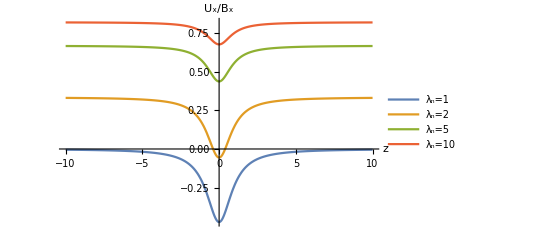
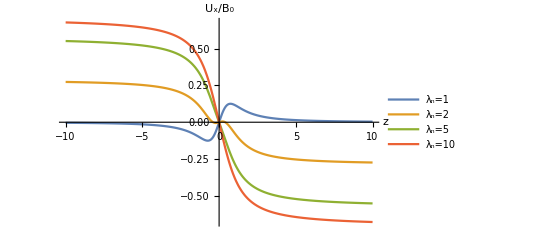
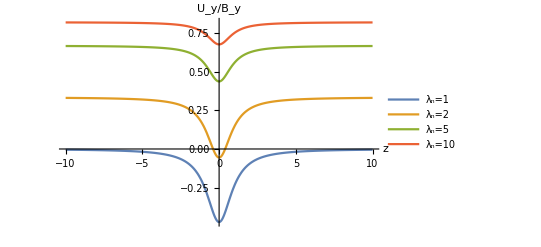
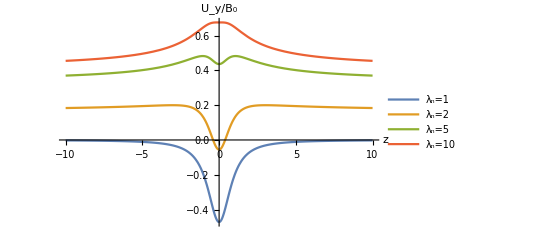

```mathematica
exps={ux/(Bx/√n), ux/(B0/√n),uy/(By/√n),uy/(B0/√n)};
labels={"U_x/B_x","U_x/B_0","U_y/B_y","U_y/B_0"};
ps=Block[{B0=2,λzInf=-1,zmax=10},
tempRules={λnInf->λnInfList};
legends=f/@λnInfList;
tempPlot[v_,ylabel_]:=Plot[
Evaluate[v/. sols//.rulesn/.Last@ condRule2/.tempRules],{z,-zmax,zmax},
PlotLegends->legends,AxesLabel->{"z",ylabel}
];
MapThread[tempPlot,{exps,labels}]
]
ExportP["UxNorm",ps[[2]]];
ExportP["UyNorm",ps[[4]]];
```

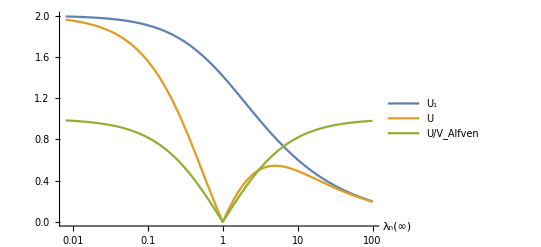

```mathematica
Block[{B0=2,λzInf=-1,zmax=10,tempExps},
tempRules= z->1000;
exp={Abs@u1,uu,uu/(B0/√n)};
tempExps=Simplify[exp/.sols//.rulesn/.condRule2/.tempRules];
p=LogLinearPlot[tempExps,{λnInf,0.008,100},PlotLegends->{"U_1",HoldForm[U],"U/V_Alfven"},AxesLabel->{"λ_n(∞)",None}];
saveP["vRatios",p];
p
]
```

```mathematica
(*Define the system of equations*)
eq1:=D[Bx[z],z]==n1[z] u1y[z]+n2 u2y-GammaE By[z]/Bz;
eq2:=D[By[z],z]==-n1[z] u1x[z]-n2 u2x+GammaE Bx[z]/Bz;
eq3:=Gamma1 D[u1x[z],z]==n1[z] u1y[z] Bz-Gamma1 By[z];
eq4:=Gamma1 D[u1y[z],z]==Gamma1 Bx[z]-n1[z] u1x[z] Bz;
eq5:=D[(Gamma1^2/n1[z]+C1 n1[z]^γ/2),z]==n1[z] (u1x[z] By[z]-u1y[z] Bx[z]-Te/(2 ne) D[ne,z]);
ne:=n2+ n1[z];


u1xInf:=Gamma1 BxInf/(n1Inf Bz)
u1yInf:=Gamma1 ByInf/(n1Inf Bz)
bc1=Bx[zmin]==0;
bc2:=n1[zmax]==n1Inf+eps;
bc3:=Bx[zmax]==1-eps;
bc4:=By[zmax]==ByInf+eps;
bc6:=u1y[zmax]==u1yInf+eps;
bc5:=u1x[zmax]==u1xInf+eps;

BxInf=1;
γ=5/3;
zmax=10;
eps=0.01;
```